Your Title Here

```mathematica
pvL={(*{vL, P},*){18.79,0.1},{20.41,1.1},{21.28,2.1},{21.99,3.1},{22.63,4.1},{23.23,5.1},{23.83,6.1},{24.41,7.1},{25.,8.1},{25.61,9.1},{26.23,10.1},{26.88,11.1},{27.57,12.1},{28.3,13.1},{29.08,14.1},{29.94,15.1},{30.90,16.1},{31.99,17.1},{33.29,18.1},{34.89,19.1},{36.99,20.1},{40.14,21.1},{40.59,21.2},{41.09,21.3},{41.64,21.40},{42.28,21.5},{43.02,21.6},{43.91,21.7},{45.01,21.8},{46.45,21.90},{48.72,22.},{55.95,22.06}};
```

```mathematica
pvV={(*{vV, P},*){30517.,0.1},{29162.,0.106},{27162.,0.114},{25162.,0.124},{23162.,0.134},{21162.,0.148},{19162.,0.165},{17162.,0.185},{15162.,0.211},{13162.,0.246},{11162.,0.293},{9162.,0.361},{7162.,0.47},{5162.,0.665},{4662.,0.74},{4162.,0.834},{3662.,0.954},{3162.,1.113},{2662.,1.331},{2162.,1.651},{1662.,2.162},{1162.,3.1},{874.2,4.1},{695.89,5.1},{574.14,6.1},{485.45,7.1},{417.78,8.1},{364.29,9.1},{320.84,10.1},{284.72,11.1},{254.12,12.1},{227.77,13.1},{204.73,14.1},{184.31,15.1},{165.94,16.1},{149.19,17.1},{133.63,18.1},{118.83,19.1},{104.18,20.1},{88.27,21.1},{86.47,21.2},{84.61,21.3},{82.65,21.40},{80.59,21.5},{78.38,21.6},{75.98,21.7},{73.29,21.8},{70.10,21.90},{65.71,22.},{55.95,22.06}};
```

```mathematica
PV=ListLogLogPlot[{pvL,pvV},Joined->True,PlotStyle->{{Thick,Black}}];
```

```mathematica
R=8.314;Pc=22.12;Tc=647.3;κ=0.8732;
```

```mathematica
A[T_,P_]:=0.4572355289*(1+κ*(1-√(T/Tc)))^2*(Tc/T)^2*P/Pc;
```

```mathematica
B[T_,P_]:=0.0777960739*Tc/T*P/Pc;
```

```mathematica
Z[T_,P_]:=Module[{a2,a1,a0,p,q,r,x,zlist},
a2=B[T,P]-1;
a1=A[T,P]-3*B[T,P]^2-2*B[T,P];
a0=-(A[T,P]*B[T,P]-B[T,P]^2-B[T,P]^3);
p=(3*a1-a2^2)/3;
q=(2*a2^3-9*a2*a1+27*a0)/27;
r=q^2/4+p^3/27;
x=If[r>0,{CubeRoot[-q/2+√r]+CubeRoot[-q/2-√r]},Module[{m,θ},m=2*√(-p/3);θ=ArcCos[(3*q)/(p*m)]/3;{m*Cos[θ],m*Cos[θ+4*π/3],m*Cos[θ+2*π/3]}]];
zlist=x-a2/3;
DeleteDuplicates@{First@zlist(*V*),Last@zlist(*L*)}];
```

```mathematica
V[T_,P_]:=Z[T,P]*R*T/P;
```

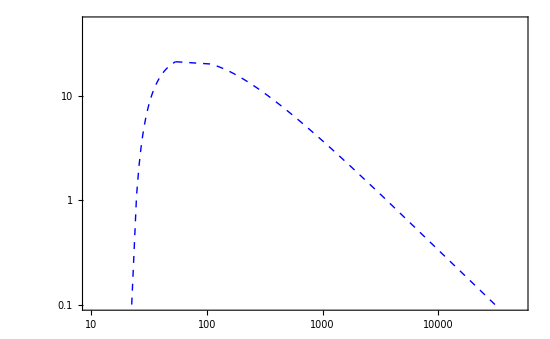

```mathematica
Module[{a,b,c,Tsat},
a={3.55959,5.40221,5.20389,5.0768,5.08354,6.20963,4.6543};
b={643.748,1838.675,1733.926,1659.793,1663.125,2354.731,1435.264};
c={-198.043,-31.737,-39.485,-45.854,-45.622,7.559,-64.848};

Tsat[P_,n_]:=t/.Quiet@Solve[10*P==10^(a-b/(t+c))[[n]],t][[1]];

(*Show[
Table[ListLogLogPlot[{{First@V[Tsat[#,i],#],#}&/@Range[0.1,Pc+10],{Last@V[Tsat[#,i],#],#}&/@Range[0.1,Pc+10]},Joined->True,PlotStyle->{{Thick,{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9]}[[i]]}}],
{i,1,Length@a}],
PV,
Axes->False,Frame->True,ImageSize->550,PlotRange->Log@{{10,5*^4},{0.1,50}},PlotRangePadding->None];*)

Show[
ListLogLogPlot[{{First@V[Tsat[#,3],#],#}&/@Range[0.1,Pc-1],{Last@V[Tsat[#,3],#],#}&/@Range[0.1,Pc-1]},Joined->True,PlotStyle->{{Thick,Dashed,Blue}}],
(*PV,*)
Axes->False,Frame->True,ImageSize->550,PlotRange->Log@{{10,5*^4},{0.1,50}},PlotRangePadding->None]
]
```

{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9]}





```mathematica
Hue@#&/@Range[0,0.9,0.1]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX